```mathematica
[-Graphics-](https://mipt.ru/education/chair/theoretical_mechanics/courses/haos-i-kotiki.php)[-Graphics-](https://t.me/miptdesign)-Graphics-mailto: efimov.ss@phystech.eduNonemailto: efimov.ss@phystech.eduHyperlinkHyperlinkActive
```

# Решение дифференциального уравнения (с первого семинара)

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

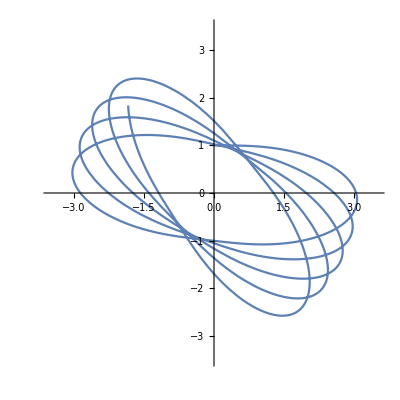

```mathematica
F[r_]:=-1/r+1/r^2;

sol=NDSolve[{x''[t]==F[r]*x[t]/r,x[0]==0, x'[0]==1, y''[t]==F[r]*y[t]/r,y[0]==1, y'[0]==0}/.{r-> √(x[t]^2+y[t]^2)},{x[t],y[t]},{t,0,100}]
{{x[t]->InterpolatingFunction[…][t],y[t]->InterpolatingFunction[…][t]}}
plot=ParametricPlot[{sol[[1,1,2]],sol[[1,2,2]]},{t,0,100},PlotRange->3.5{{-1,1},{-1,1}}]
```

# Растровая графика в Wolfram Mathematica

```mathematica
tab1=({{1, 0.5, 0}, {0.5, 1, 0.5}, {0, 0.5, 0}})
Image[tab1]
```

{{1,0.5,0},{0.5,1,0.5},{0,0.5,0}}

-Graphics-

```mathematica
im=-Graphics-;
ImageData[im]
```

{{{0.00392157,0.,0.,0.},{0.00392157,0.,0.,0.},{0.00392157,0.,0.,0.},{0.00392157,0.,0.,0.},192,{0.243137,0.203922,0.156863,0.},{0.243137,0.203922,0.156863,0.},{0.243137,0.203922,0.156863,0.},{0.243137,0.203922,0.156863,0.}},198,{1}}
 |  |  |  |

```mathematica
im2=Image@Table[Nest[k #(1-#)&,x0,100],{x0,0,0.5,.001},{k,3.5,4,0.001}]
```

-Graphics-

# Векторная графика в Wolfram Mathematica

```mathematica
Graphics[{White,Dashed,Circle[{0,0},1],Yellow,EdgeForm[{Orange,Thickness[0.01]}],Disk[{0,0},.1],Inset[im,{0.5,0},{100,100},0.2]},Background->Darker[Blue,.8]]
```

-Graphics-

```mathematica
plot
FullForm[plot]
```

-Graphics-

Graphics[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],AbsoluteThickness[1.6],FaceForm[Opacity[0.3]],RGBColor[0.368417,0.506779,0.709798]],Line[List[List[0.,1.],List[0.0306698,1.],List[0.0613395,0.999999],1794,List[-1.83638,1.82187],List[-1.83717,1.84134]]]],"Charting`Private`Tag$4861#1"]]],List[1]]
 |  |  |  |

```mathematica
RGBColor[0.368417,0.506779,0.709798]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
pts=0.3{sol[[1,1,2]],sol[[1,2,2]]}/.t->#&/@Subdivide[0,100,300]; (*построение линии из решения*)
opc=Opacity[#,White]&/@Subdivide[0,1,300];
Graphics[{White,Dashed,Circle[{0,0},1],Yellow,EdgeForm[{Orange,Thickness[0.01]}],Disk[{0,0},.1],White,Thickness[0.01],Dashing[None],Line[pts,VertexColors->opc],Inset[im,pts⟦-1⟧,{100,100},0.2]},Background->Darker[Blue,.8],PlotRange->1.1{{-1,1},{-1,1}}]
```

-Graphics-

```mathematica
Pic[t1_]:=Module[{pts,opc,npoints},
npoints=100;
pts=0.3{sol[[1,1,2]],sol[[1,2,2]]}/.t->#&/@Subdivide[Max[t1-10,0],t1,npoints];
opc=Opacity[#,White]&/@Subdivide[0,1,npoints];
Graphics[{White,Dashed,Circle[{0,0},1],Yellow,EdgeForm[{Orange,Thickness[0.01]}],Disk[{0,0},.1],White,Thickness[0.01],Dashing[None],Line[pts,VertexColors->opc],Inset[im,pts⟦-1⟧,{100,100},0.2]},Background->Darker[Blue,.8],PlotRange->1.1{{-1,1},{-1,1}}]
];
```

```mathematica
Manipulate[Pic[t],{t,0,100}]
```

# Экспорт изображений

```mathematica
Directory[]
```

```mathematica
SetDirectory@NotebookDirectory[]; (*выбор рабочей папки*)
Directory[]
FileNames[]
(*im=Import["mercury.png"];*)
```

```mathematica
(*экспорт растеризованного векторного изображения*)
Export["raster.png",im2,"png"]
```

raster.png

```mathematica
(*экспорт векторного изображения (с добавлением осей)*)
Export["vector.pdf",Show[{Pic[20]},Frame->True],"pdf"]
```

vector.pdf

```mathematica
(*экспорт растеризованного векторного изображения*)
Export["vector2raster.png",Rasterize[Pic[20],ImageSize->400],"png"]
```

vector2raster.png

```mathematica
Pic1[t1_]:=Pic[100 t1]; (*перепараметризация анимации в интервал t1∈[0,1]*)

(*покадровый экспорт анимации*)
dirname="animation_frames";
size=400;
time=10;
fps=25;

Nframes=Ceiling[fps time];
SetDirectory@NotebookDirectory[];
Quiet@CreateDirectory[dirname];
Export[
dirname<>"//frame"<>StringPadLeft[ToString[#-1],4,"0"]<>".png",Rasterize[Pic1[(#-1)/(Nframes-1)],ImageSize->size],"png"]&/@Range[Nframes];
```